```mathematica
e=1;
m=2;
P=8;
Ep=1000;
W$=Table[0,{i,1,Ep}];
WMG=Table[0,{i,1,Ep}];
WBG=Table[0,{i,1,Ep}];
```

```mathematica
(Label[New];
n1=1;"$ player";
n2=1;"MG player";
n3=99;"Back ground";
n=n1+n2+n3;
T=399;"odd steps needs";
mu=Table[0,{i,1,T}];
normalize=1/(√n);
S=2;
t=3;
mu⟦1⟧=RandomInteger[P-1];
mu⟦2⟧=RandomInteger[P-1];
signal=0;
"bestStrategy⟦i⟧,U⟦i,s⟧";"Side⟦i,bestStrategy⟦i⟧,mu⟧-->From book";
"StategySpace-->we don't construck it";
"Action=List[IntegerDigits[StrategyPosition=RandomInteger[{0,2^(2^m)-1}],2,4]]";
"AgentStrategy⟦i,s⟧--> i^thagents and the s^th strategy";
PayoffFunction=Table[0,{i,1,n},{s,1,S}];
A=Table[0,{i,1,T}];
nM=Table[0,{i,1,T}];
bestStrategy=Table[0,{i,1,n},{j,1,2}];"bestStrategy⟦Fresh,React⟧";
BS=Table[0,{i,1,n},{j,1,2}];
U=Table[1,{i,1,n},{i,1,S}];
Price=Table[0,{i,1,T}];
Price⟦2⟧=Price⟦1⟧=10;"Resource level {C_i(0),n_i(0)}={n*p(0),n-1},n=10";
c=Table[100,{i,1,n}];
ΔcM=Table[0,{i,1,T}];
NStock=Table[9,{i,1,n},{i,1,2}];
W=Table[190,{i,1,n}];
AgentStrategy=Table[0,{i,1,n},{i,1,S}];
Tinfor=Table[0,{i,1,P}];
Onetimes=Table[0,{i,1,P}];
CondionPinfor=Table[0,{i,1,P}];
ActionRecord=Table[0,{i,1,T}];
"initial set";
Do[
Action=List[IntegerDigits[StrategyPosition=RandomInteger[{0,2^P-1}],2,P]];
Do[Action⟦1,k⟧=(2*Action⟦1,k⟧-1),{k,1,P}];
RandomStrategy=Action;
AgentStrategy⟦i,s⟧=Flatten[RandomStrategy,1],{s,1,S},{i,1,n}]
Do[AgentStrategy⟦i,s⟧=AgentStrategy⟦1,s⟧,{s,1,S},{i,2,n1+n2}];
Do[bestStrategy⟦i,1⟧=RandomChoice[Select[Table[If[U⟦i,s⟧≥Max[U⟦i⟧],AgentStrategy⟦i,s⟧],{s,1,S}],ListQ]],{i,1,n}];
Do[bestStrategy⟦i,2⟧=bestStrategy⟦i,1⟧,{i,1,n}];
Do[BS⟦i,1⟧=Table[-bestStrategy⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{k,1,P}],{i,1,n1}];
Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,n1,n}];
Label[begin];
"Nature choice";
mu⟦t⟧=RandomInteger[P-1];
"mu⟦t⟧=Mod[2*mu⟦t-1⟧+signal,P]";
"group I,II  Agents choice s_i^*(t)=argmax{U_(i, s)(t)}  ,sent order";
Do[bestStrategy⟦i,2⟧=bestStrategy⟦i,1⟧,{i,1,n}];
Do[BS⟦i,2⟧=BS⟦i,1⟧,{i,1,n}];
Do[bestStrategy⟦i,1⟧=RandomChoice[Select[Table[If[U⟦i,s⟧≥Max[U⟦i⟧],AgentStrategy⟦i,s⟧],{s,1,S}],ListQ]],{i,1,n}];
If[OddQ[t],Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,1,n1}];
,
Do[BS⟦i,1⟧=Table[-bestStrategy⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{k,1,P}],{i,1,n1}]];
Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,n1+1,n}];
ActionRecord⟦t⟧={BS⟦1,1⟧⟦mu⟦t⟧+1⟧,BS⟦2,1⟧⟦mu⟦t⟧+1⟧};
"Market interaction A(t)=Σ_(i = 1)^na_(i, s*)(t)
Market Maker n_M(t)=-Σ_(t = 3)^(t - 1)A(t)";
MarketAction=0;
Do[MarketAction=MarketAction+BS⟦i,1⟧⟦mu⟦t⟧+1⟧,{i,1,n}];
A⟦t⟧=MarketAction;
nM⟦t⟧=(nM⟦t-1⟧+(-A⟦t-1⟧));
"signal=UnitStep[MarketAction]";
"Price/Cash/Wealth update deal t+1 ";
Price⟦t⟧=Price⟦t-1⟧+normalize*(A⟦t-1⟧);
If[t==3,
Do[W⟦i⟧=190,{i,1,n}];
Do[c⟦i⟧=100,{i,1,n}];
Do[NStock⟦i,2⟧=9,{i,1,n}];,Do[c⟦i⟧=c⟦i⟧-BS⟦i,2⟧⟦mu⟦t-1⟧+1⟧(Price⟦t⟧);W⟦i⟧=W⟦i⟧+NStock⟦i,1⟧*(Price⟦t⟧-Price⟦t-1⟧);
c⟦i⟧=N[c⟦i⟧],{i,1,n}];
Do[NStock⟦i,1⟧=NStock⟦i,2⟧;
NStock⟦i,2⟧=NStock⟦i,1⟧+BS⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{i,1,n}];
];
ΔcM⟦t⟧=+A⟦t-1⟧*Price⟦t⟧;
"Agents learning Payoff g_(i, s)(t)=0,odd,g_(i, s)(t)=a_(i, s)(t-1)A(t),even g_(i, s)(t)=-a_(i, s)(t)A(t)";
If[OddQ[t],Do[PayoffFunction⟦i,s⟧=0,{s,1,S},{i,1,n1}];,
Do[PayoffFunction⟦i,s⟧=(AgentStrategy⟦i,s⟧⟦mu⟦t-1⟧+1⟧)(A⟦t⟧),{s,1,S},{i,1,n1}];]
Do[PayoffFunction⟦i,s⟧=-(AgentStrategy⟦i,s⟧⟦mu⟦t⟧+1⟧)(A⟦t⟧),{s,1,S},{i,n1+1,n}];
Do[U⟦i,s⟧=U⟦i,s⟧+PayoffFunction⟦i,s⟧,{s,1,S},{i,1,n}];
t=t+1;
"Go on or Stop";
If[t>T,Goto[sample],Goto[begin]];
Label[sample];
W$⟦e⟧=W⟦1⟧;
WMG⟦e⟧=W⟦2⟧;
WBG⟦e⟧=Mean[W⟦3;;n⟧];
e=e+1;
If[e>Ep,Break,Goto[New]];)//AbsoluteTiming
```

{3745.07521,Null}

```mathematica
nM⟦T⟧
```

-20

```mathematica
W$-190//N
WBG-190//N
```

{20.3983,53.8315,11.6419,-9.45285,-19.4032,-21.3933,-30.7466,-58.4087,35.3238,83.4836,-40.1,-41.6921,-36.3189,-45.2742,21.9903,61.3938,62.9859,53.8315,-44.0801,-56.8166,-32.1397,-3.88065,16.4181,-4.07965,24.5774,43.8811,-7.66179,-4.27866,-54.8265,4.27866,100.2,0.696526,-15.2241,3.48263,-39.702,74.9263,39.901,148.957,-13.632,14.428,-15.2241,51.6424,71.1452,-34.7268,18.6072,21.5923,-89.8519,11.4429,-40.697,-20.5973}

{-116.016,-54.6637,-66.2805,-35.8947,-122.322,-134.281,-53.5782,-86.6517,-61.9265,-72.3975,-42.8117,-98.0594,-179.972,-113.562,-92.8028,-37.6878,-43.5696,-40.1844,-125.603,-69.0787,-122.666,-103.772,-97.5046,-114.237,-74.1825,-16.398,-37.2817,-80.8845,-138.554,-98.5378,-81.6684,-86.8848,-98.4313,-102.269,-121.83,-35.7842,-49.6785,-11.2037,-122.986,-86.2657,-124.154,-81.8272,-12.3435,-135.316,-30.7145,-68.7088,-84.6958,-90.1654,-104.327,-68.8636}

```mathematica
N[ΔCi,5]
N[niad,5]
N[Δnp,5]
```

{{-10.9454,-3086.27,-14502.},{-9.95037,543.577,-17076.},{-8.35831,294.926,-16973.},{-53.533,2226.07,-17318.},{-6.36824,4290.35,-17567.}}

{{7.1643,7.1643,723.59},{-50.15,-50.15,-5065.1},{34.03,34.03,3437.1},{-16.12,-16.12,-1628.1},{32.239,32.239,3256.2}}

{{0,3217.2,86.368},{0,-416.21,-247.96},{0,-330.75,523.68},{0,-2101.5,-147.76},{0,-5378.5,488.96}}

```mathematica
N[Table[ΔCi⟦i⟧+niad⟦i⟧+Δnp⟦i⟧,{i,1,5}],5]
```

{{-3.78114,138.111,-13692.},{-60.1002,77.2149,-22389.},{25.672,-1.79107,-13012.},{-69.6526,108.459,-19093.},{25.871,-1055.93,-13822.}}

```mathematica
3739/60//N
```

62.3167

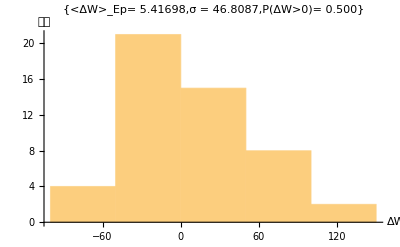

```mathematica
Histogram[W$-190,AxesLabel->{ΔW,次數},PlotLabel->{ "<ΔW>_Ep= "<>ToString[N[Mean[W$-190]]],"σ = "<>ToString[N[StandardDeviation[W$-190]]],"P(ΔW>0)= "<>ToString[N[1/Ep Total[UnitStep[W$-190]],3]]}]
```

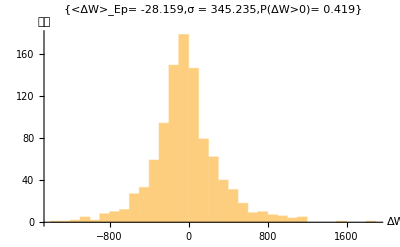

```mathematica
Histogram[WMG-190,AxesLabel->{ΔW,次數},PlotLabel->{ "<ΔW>_Ep= "<>ToString[N[Mean[WMG-190]]],"σ = "<>ToString[N[StandardDeviation[WMG-190]]],"P(ΔW>0)= "<>ToString[N[1/Ep Total[UnitStep[WMG-190]],3]]}]
```

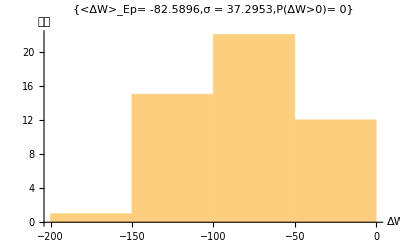

```mathematica
Histogram[WBG-190,AxesLabel->{ΔW,次數},PlotLabel->{ "<ΔW>_Ep= "<>ToString[N[Mean[WBG-190]]],"σ = "<>ToString[N[StandardDeviation[WBG-190]]],"P(ΔW>0)= "<>ToString[N[1/Ep Total[UnitStep[WBG-190]],3]]}]
```